Άσκηση 2Β_1

Τεχνητός δορυφόρος κινείται σε τροχιά γύρω από τη Γη, για την οποία σε κανονικοποιημένες μονάδες ισύει G M=1. Επίσης θεωρούμε την κανονικοποιημένη απόσταση R_ΓΗΣ=1. Σε κάποια χρονική στιγμή t=0 βρίσκεται στην αρχική θέση με ταχύτητα

r_0=2.0i+0.0j, u_0=0.5i+0.5j

ως προς ένα συγκεκριμμένο αδρανειακό σύστημα αναφοράς Oxy.

Βρείτε τα τροχιακά μεγέθη a, e, ω, για t=0 καθώς και τις αρχικές ανωμαλίες f, M και E. Επίσης προσδιορίστε την περίοδο της τροχιά T.

Θέτουμε για τις κανονικοποιημένες συντεταγμένες μ=G M=1 και R_ΓΗΣ=1.

```mathematica
ClearAll["Global`*"]
μ=1;Rgis=1;
```

Είναι a=-μ/(2C), όπου μ=G M, και C=1/2 u^2-μ/r η ενέργεια ανά μονάδα μάζας.

Υπολογίζουμε την ενέργεια για τις αρχικές μας συνθήκες

```mathematica
r0={2,0,0};
u0={1/2,1/2,0};
c=1/2 Norm[u0]^2-μ/Norm[r0];
StringForm["C = ``",c]
```

C = -1/4

και έπειτα υπολογίζουμε τον μεγάλο ημιάξονα της έλλειψης της τροχιάς.

```mathematica
a=-μ/(2c);
StringForm["a = ``",a]
```

a = 2

Για την εκκεντρότητα είναι e = √(1+(2c h^2)/μ^2), όπου h = r × u το ολοκλήρωμα της στροφορμής.

```mathematica
h=Norm@Cross[r0,u0];
StringForm["h = ``",h]
e=√(1+(2c h^2)/μ^2);
StringForm["e = ``",e]
```

h = 1

e = 1/(√2)

Για τον υπολογισμό της γωνίας των αψίδων υπολογίζουμε την γωνία στην οποία βρίσκεται αρχικά ο δορυφόρος στην αρχή του χρόνου στο σύστημα αναφοράς xy από την εξίσωση της τροχιάς r(θ)=(a(1-e^2))/(1+e cosθ).
Η γωνία αυτή είναι και η γωνία των αψίδων, γιατί είναι αυτη που σχηματίζει ο δορυφόρος με τον μεγάλο ημιάξονα.

```mathematica
th0=ArcCos[(a(1-e^2)-Norm[r0])/(e Norm[r0])];
StringForm["θ(0) = Cell["±"]``",th0]
```

θ(0) = Cell["±"](3 π)/4

```mathematica
w=-th0;
StringForm["ω = ``",w]
```

ω = -(3 π)/4

Το ότι η τροχιά περνάει μέσα από την Γη σημαίνει ότι η κίνηση δεν θα είναι περιοδική, αντιθέτως ο δορυφόρος θα προσκρούσει κάποια στιγμή στην επιφάνεια της Γης.

Δεν μπορώ να βρω κάποιο λάθος στους υπολογισμούς - ίσως να μην είναι καλή η αρχική ταχύτητα;

Από τις δύο λύσεις της θ(0) κρατάμε την αρνητική, γιατί έτσι βγαίνει η ταχύτητα εφαπτόμενη στην τροχιά στις αρχικές συνθήκες.

Αντίστοιχα, για τα f(0), E(0), M(0) είναι cos(E) = (a-r)/(a e), cos(ω+f)=(x cos(Ω)+y sin(Ω))/r, M=E-e sin(E).
Επειδή η τροχιά βρίσκεται πάνω στο επίπεδο xy, η γωνία Ω (γωνία κλίσης του επιπέδου της κίνησης από το επίπεδο xy) είναι μηδέν.

```mathematica
EE0=ArcCos[(a-Norm[r0])/(a e)];
StringForm["E(0) = ``",EE0]
f0=-th0;
StringForm["f(0) = ``",th0]
M0=EE0-e Sin[EE0];
StringForm["M(0) = ``",M0]
```

E(0) = π/2

f(0) = (3 π)/4

M(0) = -1/(√2)+π/2

Τέλος, η περίοδος της τροχιάς υπολογίζεται από τον τύπο T^2=(4 π^2)/μ a^3.

```mathematica
T=√(4 π^2 a^3/μ);
StringForm["T = ``",T]
```

T = 4 √2 π

Ποια είναι η ελάχιστη και η μέγιστη απόσταση του δορυφόρου από τη Γη και ποια είναι η ταχύτητά του σε αυτές τις θέσεις;

Το περίγειο και το απόγειο θα είναι σε αποστάσεις:

```mathematica
r[th_]:=(a(1-e^2))/(1+e Cos[th-w]);
rmin=r[w];
rmax=r[w+π];
StringForm["r_min = ``\nr_max = ``",FullSimplify@rmin,FullSimplify@rmax]
```

r_min = 2-√2
r_max = 2+√2

Η ταχύτητα σε κάθε σημείο της τροχιάς δίνεται από τις {ẋ=-(n a)/(√(1-e^2))sin f
ẏ=(n a)/(√(1-e^2))(e+cos f), όπου n=(2π)/T.

```mathematica
n=2π/T;
up=n a √((1+e)/(1-e));
ua=n a √((1-e)/(1+e));
StringForm["H ταχύτητα στο περίγειο είναι u_p = ``.",N@up]
StringForm["H ταχύτητα στο απόγειο είναι u_a = ``.",N@ua]
```

H ταχύτητα στο περίγειο είναι u_p = 1.70711.

H ταχύτητα στο απόγειο είναι u_a = 0.292893.

Ποια η τιμή των f, M και E μετά από χρόνο t=T/4;

Από τη σχέση t=τ-√(a^3/μ)(E-e sin E), επειδή για χρόνο 0 γνωρίζουμε το E(0), υπολογίζουμε τον χρονο τ.

```mathematica
τ=√(a^3/μ)(e Sin[EE0]-EE0)//FullSimplify;
StringForm["τ = ``",τ]
```

τ = 2-√2 π

Με χρήση της ίδιας σχέσης τώρα υπολογίζουμε την E(T/4), της M=E-e sin(E) τη M, και της cos f=(cos E-e)/(1-e cos E) την f.

```mathematica
ET4=FindRoot[T/4==τ+√(a^3/μ)(ET4-e Sin[ET4]),{ET4,1}][[1,2]];
StringForm["E(T/4) = ``",ET4]
MT4=ET4-e Sin[ET4];
StringForm["M(T/4) = ``",MT4]
fT4=ArcCos[(Cos[ET4]-e)/(1-e Cos[ET4])];
StringForm["f(T/4) = ``",fT4]
```

E(T/4) = 2.72234

M(T/4) = 2.43449

f(T/4) = 2.9658

Λύστε την εξίσωση του Kepler αριθμητικά και σχεδιάστε τα x(t), y(t), u_x(t),u_y(t) για μια περίοδο.

Η εξίσωση του Kepler είναι η n(t-τ)=E-e sin E. Λύνουμε αριθμητικά και πέρνουμε μία λίστα τιμών της E που αντιστοιχούν σε διαδοχικές χρονικές στιγμές, με βήμα Τ/Νpoints.

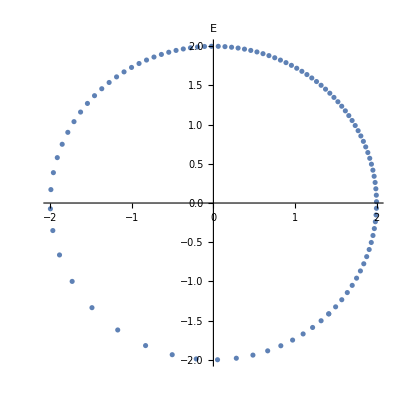

```mathematica
Npoints=100;
EE=ParallelTable[FindRoot[n(t-τ)==EE-e Sin[EE],{EE,3}][[1,2]],{t,0,T,T/Npoints}];
ts=Table[i,{i,0,T,T/Npoints}];
ListPolarPlot[Transpose@{EE+w,ConstantArray[a,{Npoints+1}]},PlotLabel->Style["E",{Bold,Large}]]
```

Τις σχεδιάζω για να επαληθεύσω ότι είναι λογικά τα αποτελέσματα.

Υπολογίζουμε την απόσταση του δορυφόρου από το κέντρο της Γης σαν συνάρτηση του χρόνου.

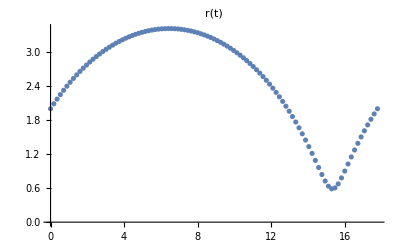

```mathematica
(* r *) rs=ParallelTable[a(1-e Cos[EE[[i]]]),{i,1,Npoints+1}];
ListPlot[Transpose@{ts,rs},PlotLabel->Style["r(t)",{Bold,Large}]]
```

1^ος τρόπος

Τα x, y υπολογίζονται από τις σχέσεις x=a (cos E-e), y=a √(1-e^2)sin E.
Οι ταχύτητες αντίστοιχα υπολογίζονται από τις

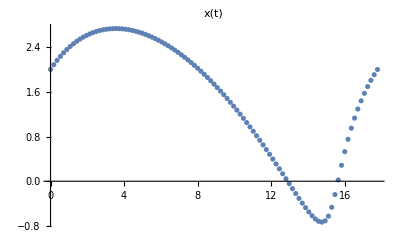

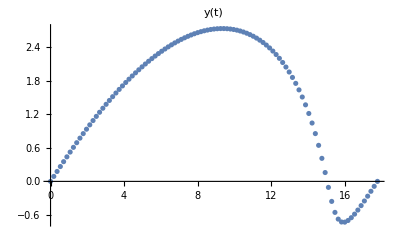

```mathematica
xys=ParallelTable[{a(Cos[EE[[i]]]-e),a √(1-e^2)Sin[EE[[i]]]},{i,1,Npoints+1}];
turn={{Cos[w],-Sin[w]},{Sin[w],Cos[w]}};
newxys=Transpose[turn.Transpose[xys]];
ListPlot[Transpose@{ts,newxys[[All,1]]},PlotLabel->Style["x(t)",{Bold,Large}]]
ListPlot[Transpose@{ts,newxys[[All,2]]},PlotLabel->Style["y(t)",{Bold,Large}]]
```

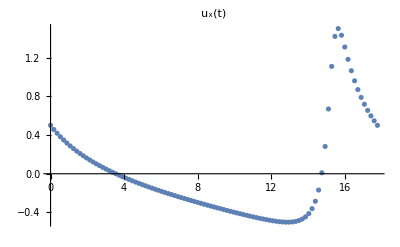

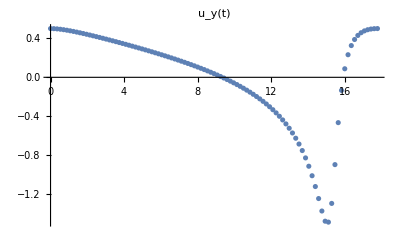

```mathematica
fsTrig=ParallelTable[{(√(1-e^2)Sin[EE[[i]]])/(1-e Cos[EE[[i]]]),(Cos[EE[[i]]]-e)/(1-e Cos[EE[[i]]])},{i,1,Npoints+1}];
A=(n a)/(√(1-e^2));
speeds=ParallelTable[{-A fsTrig[[i,1]],A(e+fsTrig[[i,2]])},{i,1,Npoints+1}];
newspeeds=Transpose[turn.Transpose[speeds]];
ListPlot[Transpose@{ts,newspeeds[[All,1]]},PlotLabel->Style["u_x(t)",{Bold,Large}]]
ListPlot[Transpose@{ts,newspeeds[[All,2]]},PlotLabel->Style["u_y(t)",{Bold,Large}]]
```

Σχεδιάστε τη τροχιά και σημειώστε πάνω σε αυτή τη θέση του δορυφόρου για t=0, t=T/4, και t=3T/4.

Χρησιμοποιούμε τους υπολογισμούς που έγιναν παραπάνω για το σχεδιασμό της τροχιάς και των σημείων που ζητούνται πάνω στην τροχιά.

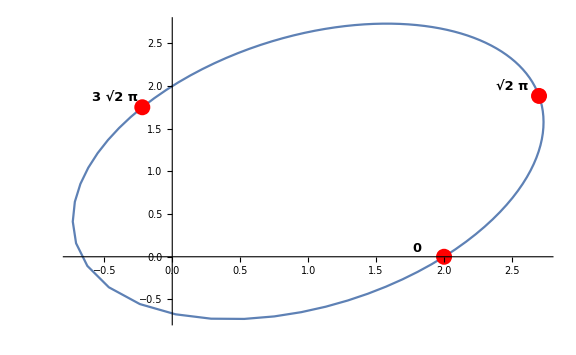

```mathematica
times={0,T/4,3T/4};
positions=Flatten@Map[First@Position[ts,x_/;x≥#]&,times];
pts={Red,PointSize[0.02],Point[newxys[[positions]]]};
labels=Table[Text[
Style[StringForm["``",times[[i]]],{Bold,Black,13}],
newxys[[positions]][[i]]+{-0.2,0.1}
],
{i,1,Length[times]}
];
ListPlot[newxys,
Joined->True,
Epilog->Flatten@{pts,labels},
ImageSize->Large
]
```

Πόσο πρέπει να αυξήσουμε το μέτρο της ταχύτητας του δορυφόρου για να διαφύγει από την βαρύτητα της Γης;

Για να ξεφύγει ο δορυφόρος απ’ τη Γη θα πρέπει η ταχύτητά του να γίνει τέτοια ώστε η ενέργειά του να γίνει μηδενική (c=1/2 u^2+μ/r), και η τροχιά να γίνει παραβολική.

```mathematica
Solve[0==1/2 u^2-μ/Norm[r0],u]
```

{{u→-1},{u→1}}